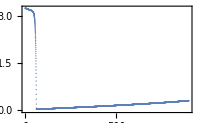

```mathematica
TheImageSize=200;
ExportAndShow["R(v)",ListPlot[{VvecSkipped,RTable[[;;,-1]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"v","R(v,u=-60)"},ImageSize->TheImageSize]]
```

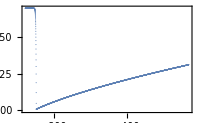

```mathematica
ExportAndShow["R(u)",ListPlot[{UvecSkipped,RTable[[-1,;;]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->MaTeX/@{"u","R(v=900,u)"},ImageSize->TheImageSize]]
```

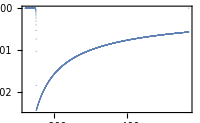

```mathematica
ExportAndShow["Tuu(u)",ListPlot[{UvecSkipped[[2;;]],cu[[-1,2;;]]}//Transpose,PlotRange->All,Frame->True,FrameLabel->{MaTeX@"u",Rotate[MaTeX@"\\widetilde{T}_{uu}",-90 Degree]},ImageSize->TheImageSize]]
```

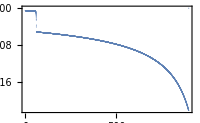

```mathematica
ExportAndShow["Tvv(v)",ListPlot[{VvecSkipped[[3;;]],cv[[3;;,-2]]}//Transpose,Frame->True,PlotRange->All,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"\\widetilde{T}_{vv}",-90 Degree]},ImageSize->TheImageSize]]
```

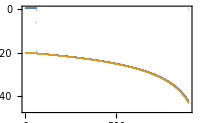

```mathematica
ExportAndShow["S,v(v) κ-",ListPlot[{{VvecSkipped,SvTable[[;;,-1]]}//Transpose,{VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,v}","-\\kappa_-^v"},ImageSize->TheImageSize]]
```

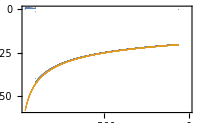

```mathematica
ExportAndShow["S,u(u) κ-",ListPlot[{{UvecSkipped,SuTable[[-1,;;]]}//Transpose,{UvecSkipped,-κm/.{m->MFunc/.{v->-Uvec0[[1;;-1;;skip]]},Q->QFunc/.{v->-Uvec0[[1;;-1;;skip]]}}}//Transpose},Frame->True,FrameLabel->{MaTeX@"u"},PlotLegends->MaTeX/@{"S_{,u}","-\\kappa_-^u"},ImageSize->TheImageSize]]
```

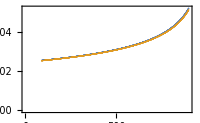

```mathematica
ExportAndShow["R,v(v) Analytical Approx",ListPlot[{{VvecSkipped[[450;;-2]],RvTable[[450;;-2,-1]]}//Transpose,{VvecSkipped[[450;;-2]],(-cv[[;;,-1]]/(κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}))[[450;;-2]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R_{,v}","-\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}"},ImageSize->TheImageSize]]
```

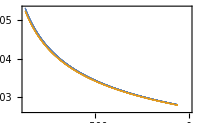

```mathematica
ExportAndShow["R,u(u) Analytical Approx",ListPlot[{{UvecSkipped[[450;;-2]],RuTable[[-1,450;;-2]]}//Transpose,{UvecSkipped[[450;;-2]],(-cu[[-1,;;]]/(κm/.{m->MFunc/.{v->-Uvec0[[1;;-1;;skip]]},Q->QFunc/.{v->-Uvec0[[1;;-1;;skip]]}}))[[450;;-2]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"u"},PlotLegends->MaTeX/@{"R_{,u}","-\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}"},ImageSize->TheImageSize]]
```